## PS 3

Sparse representations. Visualize the spatial pattern of spikes from an on-center cell with lateral inhibition

This exercise is an extension of the one in an earlier problem set where we assumed spike emission at a point is a Bernoulli trial, and the probability of eliciting a spike was proportional to intensity. The idea was to visualize a spatial pattern of spikes at an instant where there were no spatial interactions.

Our goal in the current exercise is to extend this visualization model by simulating a “snap-shot” of what an on-center, lateral inhibitory filtering of the input coming out of the retina en route to LGN might look like.  As the earlier model, this is discrete-time version of a Linear-nonlinear-Poisson (LNP) model. 

The simulation in this exercise is more representative of daytime vision, called “photopic” vision.  Imagine we could view activity across a retinotopic slice across the optic nerve after viewing the picture for an instant. There are many ways to model this and with varying complexity, for example taking into account Poisson statistics of spike rates over time (where we could be explicit about what an instant is, e.g. 100 msec), including both temporal and spatial filtering, sigmoidal non-linearities, and inhomogeneous retinal sampling. But we’ll keep it fairly simple to emphasize concepts and tools.

For this exercise, you should add two additional components to the earlier code from Problem set 2: 
	1) convolution with a linear center-surround spatial filter (as in stage 1 of the generic model); and 
	2) a threshold operation that simulates the response of an “on-center” cell (a particular form of stage 2; ).
	
	As before, you can use the ocelot image.

```mathematica
origimage=Import["ExampleData/ocelot.jpg"];
```

You can construct your own program as you wish, but it may help to try to use high-level image processing built-in functions in Mathematica as suggested in the following parts of this exercise:

a) To model lateral inhibition you can use LaplacianGaussianFilter[ ] on origimage. This will create a center-surround filter and do the convolution all in one step. Let the kernel radius = 3.0. Short-hand for this filtering operation is LoG. (Note: instead of LaplacianGaussianFilter[ ], you could do the filtering in several steps by first defining a 2D gaussian, computing its Laplacian, and using ListConvolve ).

Use ImageAdjust[ ] to normalize the filtered output to range between 0 and 1, and display the result. Call it ifiltered. It should look something like:

-Graphics-

```mathematica
radius = 3.0;
ifiltered =ImageAdjust[ LaplacianGaussianFilter[origimage, radius]]
```

-Graphics-

b) To simulate the output of an on-response unit, run the above filtered output through ImageClip[<out>,{0.5,1.0}], and again normalize the output, again using ImageAdjust[].  The idea is to set values of  ifiltered that are below a threshold of 0.5 to 0.0. And then use ImageAdjust[] to get output values to go from 0 to 1 again for visualization purposes.

(The threshold of 0.5 is arbitrary and takes advantage of the  ImageAdjust[] operation in part 1 above, which adapts to the response range by scaling the gray levels to be between 0 and 1. One could be more sophisticated and have an adaptive component to set the threshold, e.g. based on a local average. Later on we’ll see how to model a sigmoidal threshold for an integrate-and-fire neuron probabilistically.)

Call your filtered clipped response iclipped. It should look like:

-Graphics-

```mathematica
iclipped = ImageAdjust[ImageClip[ifiltered, {0.5, 1.0}]]
```

-Graphics-

c) Now adapt the same solution from problem 4 in problem set 2, but applied to the iclipped image to produce the “snap-shot” of the spiking activity:

Image[Partition[RandomVariate[BernoulliDistribution[#]]& /@ Flatten[ImageData[iclipped]],200]]

Call the image ispike. 

Use GraphicsRow[ ] to compare a) the original image b) the LoG filtered image c) the on-center response and d) the the “snap-shot” of the spiking activity.

GraphicsRow[{origimage, ifiltered, iclipped, ispike}]

```mathematica
ispike = Image[Partition[RandomVariate[BernoulliDistribution[#]]& /@ Flatten[ImageData[iclipped]],200]];
GraphicsRow[{origimage, ifiltered, iclipped, ispike}]
```

-Graphics-

Note that the ispike picture is a “spike” rather than “rate” view of retinal output. It illustrates the high degree of sparseness in the spatial pattern of spikes at an instant. (There is another class of cells--the “off” cells--that signals the negative going filtered response.) 

Sparse responses raise the question of how the richness of perceptual experience emerges from such an apparently drastic reduction in information leaving the eye.

And later we will see how sparse representations can be learned from an ensemble of sensory input patterns using unsupervised methods.

Regression and Widrow-Hoff learning

Motivation. Making estimates of higher dimensional vector outputs from lower dimensional inputs happens and is common to many so called “early vision” problems (Poggio et al., 1985; Knill and Kersten, 1990). One vision example is the “shape-from-shading” problem where each gray level pixel in an image gets mapped to a two-dimensional vector that is locally perpendicular to a surface. The collection of these two-dimensional vectors--surface normals--characterize the 3D shape of the object. The mathematical problem is under-constrained because there are twice as many parameters to estimate as there are equations from the (known) generative model. A priori solutions require a some kind of regularization or “smoothness” assumption, e.g. the assumption that nearby shape vectors tend to point in the same direction. These solutions are related to “Ridge Regression” in statistics. However, if there is enough data to associate input patterns with their higher-dimensional outputs, a linear approximation can be learned from the data. This exercise illustrates this idea with perhaps the simplest model where a single scalar outputs a 2D vector.

-Graphics-

The input data, xx,  is a list of 1D scalars, and the associated output data, yy, is a list of 2D vectors. Each input value gets mapped to two output values.

Select the tiny closed square bracket below and execute to initialize xx.

```mathematica
xx={-0.584976714087647,1.9456203080929981,-1.7728491015291663,-1.4989468039627294,-0.9015396952064352,0.1527484085409787,1.5859274054461858,1.0736990236800397,0.023978261351401464,0.39756901840406744,-0.6054443264296534,0.06053740495974047,-0.5794593649964952,1.391790328254375,-0.3687628117120374,-1.1464482010657147,0.5145055165658432,1.828198106945102,1.5886988813855032,0.34141247398380603,-1.488541970565696,-1.4015094000911272,0.4828347649612299,0.018877321976061623,-0.9034397106187875,0.8222018888269949,0.3952384330569272,1.9478269062354983,1.3143375259960015,0.8181780199048712,-1.0292268785035406,1.5313408468667884,0.029258394599270154,1.652722049620654,1.494619553356058,-1.2520813120399756,0.6234498641299568,-0.4536277121954386,-1.2227747620593368,-0.40154598535458774,0.6002071260383843,0.5339596724312923,-1.0045477164511842,-1.7796994862450752,-0.9410738856278256,-1.397853496328561,0.9238682871110635,0.9902048890886022,1.3066146195661767,-1.852146677171426,1.708174187351375,-0.3972692134344671,1.2045272333196912,-1.0545521310155461,-1.6032286023886106,-0.4225108909217479,1.5499339646962644,-1.9398174414181302,-1.366705981563876,0.5664462567964428,1.925653308503735,0.938971899801496,-1.9412318222037097,0.5635521590321861,-0.23743530187626316,-0.7548278071796837,0.31331028531564975,0.7056211790823594,1.5507138536050054,0.5596528577545197,0.826953559935526,1.7900307817062107,-1.7805208222467463,-0.8197984525727247,-0.10617256353830129,1.5469477410635024,1.3314979088628496,-1.1642545448641428,0.8825751394143948,0.5305339160854032,-1.1047182624173866,-0.5460641138973781,-1.328715052751929,-1.4596643105033973,-1.109308304252555,0.8213234451642579,1.7446322438191872,0.9022358378461846,-1.794527187944853,1.3938660756580914,0.264855244153579,-1.2413240208353624,-1.0341483141985117,-0.8062810538199958,-1.6236524310133706,-0.3527349628524643,-0.005001549986579867,-0.24754418612120244,0.10151294353328932,0.6238769751178017,-0.5039775444971637,-1.4212635017280837,-1.4454392048854086,0.03758763415111943,-0.8356056126426354,1.3527544398782432,-1.6225520400983662,-0.9973874309807673,1.0544719339976805,1.5132176601160907,0.0894554901471567,1.3809986491721595,0.2967527195566353,1.167046990283013,-0.37226953955293585,1.6967844885614944,-0.186592242272404,-1.1269921827904472,1.7883289401302056,-0.7737408364222995,1.3813505098736751,1.6943634332561217,1.925293255196256,1.6191576923297886,-0.3674323167818949,1.2145635235024503,1.8677823070997945,0.3053806143058839,-1.5570283141324248,-0.7526204810367974,1.0360101792596739,-1.1711111448596734,0.2094075467072205,-0.9526983522907857,-0.3468696473927242,-1.341423895610153,1.1483963218720428,0.5519412835648767,-1.5150164523382976,1.272914080516168,-0.3718084689609711,-0.10160184106898384,-1.4566431546982557,-1.2519210216839527,0.11826033310066464,-0.003669763067727594,1.076764641481705,-0.44761873245860784,-1.138750626498159,1.7752509559645029,-1.1746425105711662,1.8337333842870782,-1.8516471302634896,1.0037605812770414,1.9008053696694152,1.1603533082684594,-1.5393192858952283,-1.5010655440090375,-1.614040280476952,0.8164738525982527,-0.783134913682507,1.436623750277846,-0.8419961402693898,1.9334190884166196,1.5182845449511957,1.9226061941863817,0.26502903564568214,1.3234820874312465,-1.9742315117708031,-1.4255064500183048,-1.506635691245215,0.690707472387186,0.5194813186723328,-0.5600433397794289,1.4808990949600886,-0.6816714884776047,1.7541498488507434,1.9317906340352637,-0.984662518238073,-1.33347356132533,0.7924580181192766,-0.7072783165067422,-0.37979982635661536,-1.9461893565499109,1.5153494760213126,0.2166948048248729,0.7819853960748331,0.8795926078701077,1.073962109948841,-1.0431728700037697,0.09438665418435566,1.2006686292700426,-1.1433918934216551,-1.357133183852861,-0.3517474048577611,-1.9744978035672984,-0.27305218868309744,1.8960694386643837,-1.67946088219227,0.6145066447046474,-1.4169255001495715,-1.6848498309318396,1.4106208532875346,0.16517356673105965,-1.637684694381102,0.8296817413667492,1.114364101744929,0.13938473615376612,-0.736409671846264,-1.2493443626855987,-1.133135524855927,-1.3266771761035683,-0.7445216546351254,-0.6462056390242257,1.3785799781042734,-0.006595619955056975,-1.633033408423545,0.6787248449914403,-1.297351495266927,-0.11441965670630694,-1.628148302931037,-0.28372028917426917,-1.3731745847928654,0.8538870954428166,0.2203793056292973,-0.6632874098945543,-0.31492175302066183,-1.5646378178715645,-1.8817018210149978,0.3908341654990757,0.36963432224368287,-0.4514344676952122,-0.9806218498722901,0.7960038584367961,1.9769430051094972,0.14961073781453926,0.21288544161427936,1.9446753847506653,-0.3311157067810928,0.7255497016801344,-0.7690953858372502,-0.6057727508700932,-0.7223815830649123,1.0989608353737124,-1.0536232705290303,-0.6085348735429248,1.428590314104662,-0.9987973776599519,-0.0919531306743453,0.24235565241707047,-1.0591734222794935,0.1156111367024506,-0.3729234740692675,-1.5070368894397905,-0.745393568408292,-0.3474097655246773,0.14779062277353372,0.19178927242442612,-1.471578055031098,1.7990119923962515,0.07342155882719936,-1.0106951061666445,0.4307586557688605,-0.9408690598980849,-1.089180262362028,-1.8834816936382488,0.10565225079891505,-0.7251482415797712,-0.7688671946453018,-1.151496262505579,-0.06332660449512684,1.3344825004635004,0.2622069668384306,1.5423809647990403,1.9990739090567917,0.38050681696553657,0.8438955188813146,-0.40146921438132654,-0.6318351673907214,0.6052772271088651,1.6345775186309606,0.9467509037269259,1.9783268701456151,0.8564799239801886,-0.548071581900416,-0.34086880130744834,-0.4116989001131506,1.3681774419295438,-0.622845604211884,-0.7225973714675709,0.8484347356150828,0.06438377742390244,0.06013599199721931,-1.0391179695369095,1.8496445264165358,0.2981045198728838,0.7999881430742519,1.2330633986130408,-1.1281766198717555,-1.7398842760185316};
```

Execute the cell below to initialize yy

```mathematica
yy={{-0.4081356181029614,-3.3905629216129416},{6.71313751370216,13.186012879391605},{-3.533260295783225,-11.12636127768595},{-5.342530661438101,-9.169991772247648},{-3.5542434503025513,-7.1845869421807995},{0.04298843764783378,1.3577023706474556},{3.02778992706721,11.22344663014593},{2.766085499258927,6.657422284211615},{-1.8936156650861244,0.44086290123104366},{-0.34673519961023036,3.8554752185190306},{-3.206450142736326,-2.371818677261947},{0.25630080843643643,-1.3687442023831657},{-2.3534347329974263,-5.071817276598167},{5.069765970908058,9.321328512194814},{-3.0983484256427962,-2.203779579871185},{-5.07799187734754,-9.925988043724537},{0.8145800862906496,1.8469040152187812},{7.3468976603541,13.74236629994731},{4.242074406127801,10.313330573374323},{-0.9470691870245052,1.714575062229521},{-3.0877300132973664,-11.67294700920619},{-5.055796745911146,-8.134704948942755},{0.04029300864720753,1.5082910448062412},{-0.5334458015295613,0.5327739553134458},{-0.9621498124091277,-7.272077290460133},{3.187993214542513,4.781391327588373},{2.067499756717334,2.082602451985192},{7.547666183746454,14.162152747872454},{3.1352032854084344,7.825702916288718},{0.5733752316875975,7.082615757876754},{-2.454890897612855,-6.960444206042511},{6.071088909106551,9.433332260048989},{0.8135525418957945,-0.7502686111671348},{3.845035536670558,12.437160899058254},{4.773252307497492,12.404281616556514},{-3.4995034681481165,-7.520775276680536},{1.654711264406437,2.7788871257526315},{0.301123258936725,-4.2830161940347615},{-5.004778390949862,-10.19911603528061},{-2.7674127218235567,-1.3423076710820796},{3.0202942666971504,5.217902429874465},{2.1063812552117556,4.912845269088958},{-2.6210169548501927,-5.800543683433417},{-6.928099083933079,-11.490069346579478},{-1.8900214296095896,-7.549824550966419},{-4.857443045382599,-9.65821988490259},{2.516711928448088,4.929823714444769},{2.125810755680579,8.357945955267978},{5.807400866319166,9.132647280609726},{-4.1289272603662805,-11.681045914253549},{3.150633603316563,13.01613829439922},{0.2848074434796013,-4.561056467752499},{3.9433093202833156,7.319647522076515},{-3.704822749399411,-8.027778518547798},{-6.055129888464092,-12.013611810185903},{-0.3688645099625063,-1.2980064063789065},{5.617311074993334,10.59676761764366},{-4.645099726768217,-13.145884043713117},{-5.852781180608062,-7.992397542365325},{3.686895084942253,3.603479804354615},{3.929876160302295,12.576189833873501},{3.6686045315607476,4.960587019517603},{-5.052431040840374,-14.585992109115676},{1.7214228617760714,4.71674164939974},{-2.5776503040142016,-2.7197503002666394},{-0.47094983391281886,-7.177798395750379},{2.4816500708651352,2.5391358486656346},{2.0329034478079455,3.1922004116962235},{6.287402540374535,11.901806413461125},{0.9491625271881645,4.737402449130718},{2.5152944937693036,7.579619205716001},{5.193313473166285,10.948853109705455},{-3.3720594010041562,-13.533593312585973},{-1.9214045264222657,-4.094879175718143},{-2.197364251854083,-0.2887561665005869},{5.774538312515535,11.479813989577005},{2.7311409498906727,8.14569953017114},{-1.8355634011946655,-9.160676916833953},{3.7298913707849026,6.934717350058132},{1.5217226796435925,5.634054775591365},{-1.4624835090090622,-9.415962240688895},{-1.857024252003483,-3.438574456970869},{-2.8859289738162506,-9.305163974693906},{-2.587150455391667,-11.361691288855447},{-5.193557739227141,-9.524343731361292},{2.5483109703206743,5.209557361293115},{5.0591143885314445,14.030898751575336},{2.092236341804951,4.804942224842692},{-5.474839985381586,-12.143375524880756},{4.5640101948218454,10.155849110937858},{-0.7048839046085753,3.704011385706763},{-3.985169899363166,-8.533347675424096},{-1.4991325403183646,-6.7288337407366265},{-3.184821255779222,-7.061694343341643},{-4.273478781090905,-12.45325463117795},{0.11248636749530938,-1.1514032937887615},{1.1677691764407356,-1.1315657902068041},{-1.702953891784781,-0.19361247412150995},{-1.3414671055116765,2.1187132293718367},{1.1167939423534703,3.024368334108667},{0.13794437110457292,-3.1161089727552733},{-5.278944907350868,-10.25363970269424},{-3.875396154228987,-8.410727195377838},{-1.4505596336914754,0.03118603837064793},{-3.277043438887059,-6.778156456769857},{3.2126928344205794,8.660505246401202},{-4.427832556128786,-10.079572359015271},{-2.296743143157271,-6.093018566909296},{2.755238295867051,8.98240272091233},{3.831351448209028,9.341741924437091},{1.0054788075937005,2.128196181730389},{5.068520643976933,10.68361140922349},{0.8843487111792996,2.045276923060123},{5.398769814764389,8.263010913424221},{0.7111889023941744,-1.7568609951108787},{4.101046897515015,11.219619070423027},{-1.2366266904194543,-0.62445638881508},{-3.9964461011755263,-6.749192734840824},{5.839940088104258,13.824510484669872},{-3.0904166789084186,-3.7921912950529943},{5.852631910085305,10.24598726348611},{6.992038432144063,10.486302138716358},{7.180214728960954,15.07126353182936},{3.5390633522331534,12.712828465176255},{0.7685486710417262,-0.7281199266717957},{3.3949050022095006,9.619371942238836},{7.371316633495277,14.725434691850342},{1.4124602063935487,0.25625969241026514},{-4.858614753334114,-12.678906083685773},{-2.518549066427103,-6.266143954730159},{4.2267975545601395,5.670358590239054},{-4.395714038189946,-6.504205476852072},{-0.1378876625045029,0.5861631743802516},{-2.2623609310314023,-5.268045814269023},{-0.6149999961960608,-2.6778781396002076},{-2.2612811482526496,-8.745021378883777},{4.711705670646865,8.19005451206753},{2.2065743055159635,2.0535286568653595},{-3.913210565041555,-11.658283818207014},{4.9540454198455075,9.59757988132589},{-2.840482064042688,-2.1853745767414896},{0.04087923988588127,-1.5437753813356023},{-5.1059215240197116,-9.905225072618139},{-5.083345792350973,-9.496613216078522},{0.8689129889919069,0.4270488641297412},{1.6228532958226838,-1.2789549488900498},{3.860504755676695,6.388660565250207},{-2.09384826620808,-4.828049515200092},{-4.857697982152437,-8.703638049116325},{4.346490702730608,13.319856954029223},{-3.494962280717476,-7.908490188121283},{3.883437665015129,10.930851521173928},{-5.448120076671429,-11.58941795796363},{4.55047110698162,6.750007092051526},{4.1011528617962245,13.15558225484942},{3.432519192458205,6.232587093033376},{-6.142257659243657,-10.661617829594274},{-3.226741493607422,-10.550378473616085},{-4.034449924789319,-11.465972916073753},{3.5467248530509474,6.1355379683265046},{-3.278529995626724,-5.680537040856559},{4.753973395522712,8.733782861657492},{-1.5807525041279513,-6.694630569159789},{5.797726025300776,11.869619097757415},{3.5466298936492135,12.191868424271444},{4.239911632522711,15.081905158206515},{-1.1021975840912352,2.539374115419192},{4.585703273790756,8.428773131161325},{-4.011169466374354,-14.352195301802656},{-4.397684728721672,-8.20095576098613},{-5.564369937590273,-10.762561171136353},{0.6174538225366746,5.877214976034417},{0.15479687325049074,3.2688341070853575},{-0.7065300921025113,-4.885316327973237},{2.5742127863315236,12.054102248137072},{-3.74804280825905,-3.752136893450282},{3.581307883758715,12.565431209819845},{6.59143161560665,12.520795276616859},{-4.145899235302896,-7.25112753005437},{-3.7470642245434815,-11.275453443127258},{3.436135871717788,4.032411928727492},{-1.0294879860404045,-5.1006939367261115},{0.36660661618121093,-0.8776017932104896},{-7.71030767337858,-11.718485540685151},{3.5878415590106263,10.70719462556697},{-1.2655402415705526,3.2946379646477695},{4.2255666067398066,7.268524274660542},{1.2871051195666894,6.888887608790263},{4.268388180216528,6.31899897157358},{-2.490849655934186,-7.0882270411825745},{0.5807956307059703,2.4132517999203644},{5.511432251441976,6.773705876990266},{-3.3149495250750327,-9.721153134841076},{-5.0333699686727575,-8.51762048781612},{-1.1576381549844665,-1.722506929205064},{-5.277846856193769,-12.014995218300669},{0.7081094594352493,-0.3233156936557613},{3.932578600509001,12.344681765658486},{-5.494284974975803,-11.312343770569168},{3.7414439837997033,5.632661826058243},{-5.41183907630277,-10.9188769546994},{-6.777755304128525,-13.414283926394873},{2.2951313033118934,8.075754761684689},{1.437352866042577,1.4425730288088223},{-6.232105628066757,-11.63008334586171},{4.322036821777564,5.8589964707397435},{1.9486186066487141,8.240654928864029},{-1.1169439828265784,1.1625415537429546},{-2.22815130010924,-4.267382321188828},{-5.315438413260898,-6.996979195877098},{-2.514314322615422,-6.69767384513834},{-4.397394511389991,-8.793391952861771},{-3.511929476851315,-5.063877509122424},{-3.85382707223276,-4.91552998523415},{6.083097974275917,10.76915176448293},{1.947187888956,-0.6040621798370402},{-3.972577090774558,-10.372095512859293},{1.356609954190966,4.168272883179536},{-2.7969169847079485,-10.55720307736057},{1.1427530081957507,0.8054214605302104},{-5.052978307550733,-10.175506679226753},{-1.081881719043218,-1.2296014088586817},{-5.718571778389582,-7.731912878654034},{3.583834554067325,5.02549110348528},{1.2019749521458944,2.972399033774625},{-3.050576317722647,-5.570305281445896},{-1.8494720159282352,-2.6851472601182147},{-3.8514031755268743,-10.017195485929367},{-5.106795895501376,-15.04581257790526},{0.3684396657473874,3.0345546648199946},{-0.5254246399132949,2.357715113862813},{-1.7170843199313817,-1.4001471719252292},{-2.760021071758943,-6.340588672109005},{3.2671302080998066,6.109680956737997},{5.364070894457702,15.539420375232165},{2.0002148500179375,1.6162783630189699},{-0.2555169736127567,3.3944503667678845},{7.042275184324614,14.208734642454402},{0.10021827677340145,-0.9079421934168996},{2.857416756871939,6.992504752163726},{-1.367425727891261,-6.945244860143641},{-2.527936030040366,-4.790626696682257},{-2.9688844770259353,-6.352670799479892},{2.0431926765616497,8.985505620795028},{-4.226083476441672,-7.45081936413476},{-3.370892106249771,-2.9589797710674155},{6.2669277110849695,8.74294431469103},{-4.855935119552985,-7.101365708940914},{1.2407645238355798,-0.3327165326191004},{-0.017090633207600625,0.7280787017550212},{-4.9713698412184115,-7.862479185965065},{1.6687053388006428,2.1514358965215106},{-2.175296641331686,-0.9529847877545388},{-5.533778566389774,-11.971058089371738},{-2.390517510134371,-6.977538129060179},{-2.103611262662998,-1.6765677283056544},{-1.451035208350656,0.7430940238770818},{-0.673035003993089,-0.16197016235128192},{-3.135888641662156,-11.139067403303331},{5.190787261844152,14.471418227407618},{-0.008132782149559148,0.6032819087038392},{-4.485744968000661,-5.559632269299922},{2.214269124490765,4.465929074445463},{-2.4667133187141195,-5.723503361581864},{-1.3677778399765144,-7.292803629552683},{-6.4891283422860715,-13.038187329009569},{1.994785045424206,1.8648651658568909},{-2.1705141335524507,-5.711083885979806},{-0.7604381607086319,-3.493816239063592},{-4.861481253434109,-7.2225108112477265},{1.133704534657288,-1.9477190294845839},{3.842808384440512,8.122802892084959},{-0.6758687750107786,2.580817634512889},{3.4110997010782356,9.968594176122274},{6.723244184161152,14.768453091726842},{2.1667468826907177,0.8183637238585124},{4.380029555169049,5.764663454241226},{-0.523679456456529,-1.9440439009479693},{-0.6173883411292973,-2.6495706304777835},{3.027400822542927,3.889645655467489},{6.5129111898759575,11.744689517902525},{3.841662744003318,6.4092080976919785},{6.687388044369829,12.516810346090736},{4.200622839886085,4.4993346833313765},{-3.2507665387858022,-4.993724315488481},{-1.738058711969285,-2.3574649777533248},{0.43061126104138747,-2.6884017804883715},{4.300263703895264,8.249852856757279},{-1.7846181128495626,-2.525463210952058},{-3.6233571576389343,-5.183436868476631},{1.3126485183823258,5.785585434509528},{-1.6158740227363069,1.501123853127818},{0.8422261247813632,1.9378573050352523},{-2.442307356362374,-8.930767879631901},{4.97680534945566,12.589156095336733},{0.23462966828736764,1.875686738413708},{1.5161209912372486,5.320969322990818},{3.758297789549972,10.056704971682898},{-4.317734773035739,-6.630907644417221},{-5.690728002621735,-14.108431199609694}};
```

Check the dimensions of xx and yy.

```mathematica
Dimensions[xx]
Dimensions[yy]
```

{300}

{300,2}

a) Apply the Widrow-Hoff algorithm to discover a linear relationship between the input stimuli, xx, and the output responses, yy. Let w1 = {{a},{b}}. The mapping you want to discover is, given x, what is {y1, y2}? 

	 {y1, y2}  =  {{a},{b}}.{x}. 

The goal is to learn the parameters {a,b} from training pairs of inputs and outputs:  {x, {{y1, y2}}}. Feel free to adapt code from Lecture 10.

Accumulate your trial-by-trial estimates of a and b in two lists: {alist,blist}, and then use
ListPlot[{alist,blist},PlotRange→{0,20},AxesOrigin→{0,0},Joined→True] to visualize your results. 

What values are a and b converging to?

```mathematica
weights = {0, 0};
alist = {};
blist = {};
eta=.01;
j=0;
epochs= 5;
While [j<epochs,
i = 1;
While[i<=Dimensions[xx][[1]],
	x = xx[[i]];
	y = yy[[i]];
	weights = weights + eta(y-weights*x)*x;
	alist = Append[alist, weights[[1]]];
	blist = Append[blist, weights[[2]]];
	i++;
];
j++;
];
weights
```

{3.14085,6.9719}

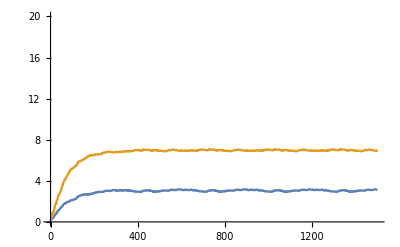

```mathematica
ListPlot[{alist,blist},PlotRange->{0,20},AxesOrigin->{0,0},Joined->True]
```

b) Use the pseudoinverse to compare the Widrow-Hoff solution to the least squares one.

```mathematica
PseudoInverse[ArrayReshape[xx, {Dimensions[xx][[1]], 1}]].yy
```

{{3.04931,6.97057}}

Use error backpropagation to learn to classify letters independent of orientation

This exercise illustrates the use of the classic “backprop” model of learning in multiple-layer perceptrons, with a very simple , not very “deep” network--just one hidden unit layer. The exercise shows how non-linear regression learning can drive outputs to threshold and saturation regions (interpreted as “false” and “true”), which allows one to do classification via a feedforward non-linear network. The application is to a “toy” version of the rotation invariance problem.  Without more structure, the backprop algorithm supplied below doesn’t scale up well to complicated real world invariance problems. For that, other methods such as deep convolutional networks, are needed. This exercise only uses a training dataset. Later we’ll see the importance of distinguishing between datasets used for training vs. testing, when searching for robust generalization.

a) Define two classes of patterns, T's and C's. Each class should have four members for rotations of 0,90,180, and 270 degrees.  To get you started, here are exemplars for T and C on a 3x3 grid:

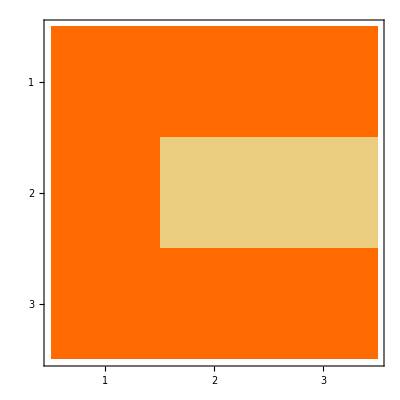

```mathematica
T1 = {{0.9,0.9,0.9},{0.1,0.9,0.1},{0.1,0.9,0.1}};
C1 = {{0.9,0.9,0.9},{0.9,0.1,0.1},{0.9,0.9,0.9}};
MatrixPlot[C1, ImageSize→Tiny]
```

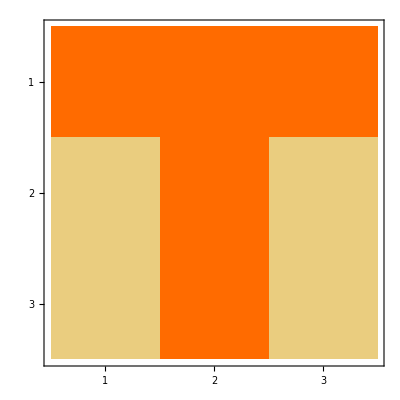
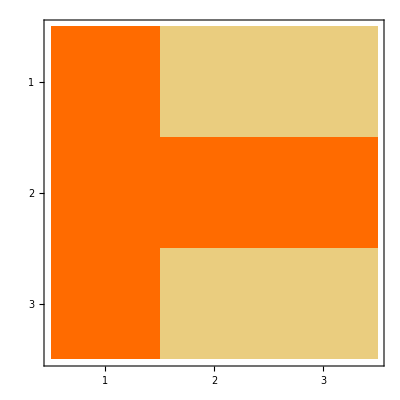
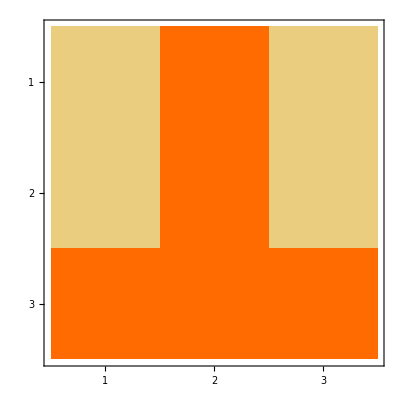
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

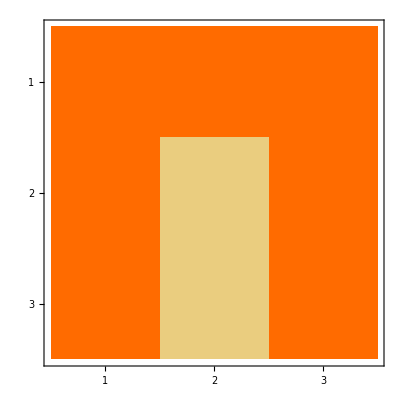
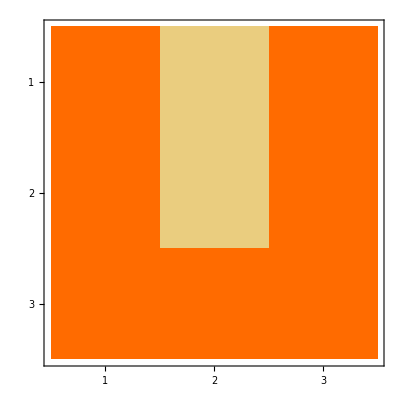
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{0.9,0.9,0.9,0.1,0.9,0.1,0.1,0.9,0.1},0},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},0},{{0.1,0.9,0.1,0.1,0.9,0.1,0.9,0.9,0.9},0},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},0},{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},1},{{0.9,0.9,0.9,0.9,0.1,0.9,0.9,0.1,0.9},1},{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},1},{{0.9,0.1,0.9,0.9,0.1,0.9,0.9,0.9,0.9},1}}

```mathematica
GetRotations[mat_]:={Flatten[mat], Flatten[Transpose[mat]], Flatten[Reverse[mat]],Flatten[Reverse[Transpose[mat]]]};
AddLabel[Letters_,label_]:=Function[{ele},{ele, label}]/@Letters;
Ts=GetRotations[T1];
Cs=GetRotations[C1];
Table[MatrixPlot[ArrayReshape[Ts[[i]], {3,3}], ImageSize->Tiny], {i, 1, 4}]
Table[MatrixPlot[ArrayReshape[Cs[[i]], {3,3}], ImageSize->Tiny], {i, 1, 4}]

(* Binary encoding for class labels: T = 0, C = 1*)
trainingData = Join[AddLabel[Ts, 0], AddLabel[Cs, 1]]
```

And here is what they look like:

-Graphics-

#### Backprop function

```mathematica
(* xshft and λ are pre-set, and control the bias and steepness, respectively*)
sigmoid[x_] :=
        Module[{xshft,yshft,λ},
                xshft =0; 
                λ= 1;
                1/(1+E^(-(x-xshft)/λ)) //N
                ]

backprop[inNumber_, hidNumber_, outNumber_,ioPairs_, η_, numIters_] :=
  Module[{errors,hidWts,outWts,ioP,inputs,outDesired,hidOuts,
                        outputs, outErrors,outDelta,hidDelta},
	hidWts = RandomReal[{-0.1,0.1},{hidNumber,inNumber}];
	outWts = RandomReal[{-0.1,0.1},{outNumber,hidNumber}];
	errors = Table[
                        (* select ioPair *)
		ioP=ioPairs[[Random[Integer,{1,Length[ioPairs]}]]];
		inputs=ioP[[1]];
		outDesired=ioP[[2]];
                        (* forward pass *)
		hidOuts = sigmoid[hidWts.inputs];
		outputs = sigmoid[outWts.hidOuts];
                        (* determine errors and deltas *)
		outErrors = outDesired-outputs;
		outDelta= outErrors (outputs (1-outputs));
		hidDelta=(hidOuts (1-hidOuts)) Transpose[outWts].outDelta;
                        (* update weights *)
		outWts += η Outer[Times,outDelta,hidOuts];
		hidWts += η Outer[Times,hidDelta,inputs];
                        (* add squared error to Table *)
		outErrors.outErrors,{numIters}];  (* end of Table *)
Return[{hidWts,outWts,errors}];
        ];
```

The above  code was adapted from: “Simulating Neural Networks with Mathematica” by James A. Freeman (1993). (Amazon link).  Original code sources available at: https://library.wolfram.com/infocenter/Books/3485/

b) Using the backprop[] function defined above, train a non-linear feedforward net with one layer of hidden units (two weight layers) to correctly classify the eight patterns as T or C.

Fix the learning constant, η,  equal to 1. What is the minimum numbers of hidden units you can find that will still converge in under 600 iterations? (Don’t change the above definitions of sigmoid or backprop). 

You can answer this question informally, but you should show that you’ve explored the space, trying several runs with the same parameters. 

For this number of hidden units, explore the range of the learning constant (η) that still allows convergence. What is your informal estimate of the maximum value of η that allows convergence?

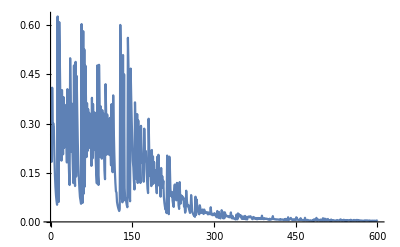

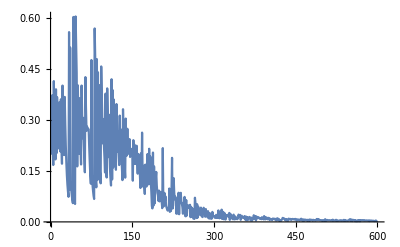

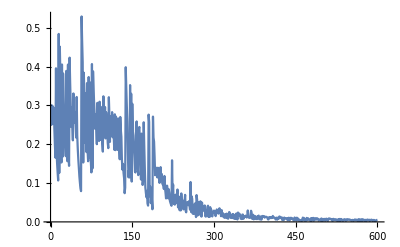

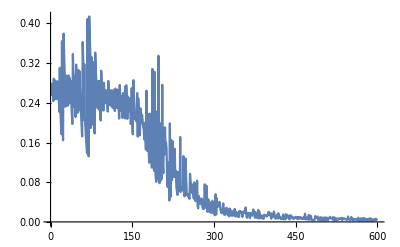

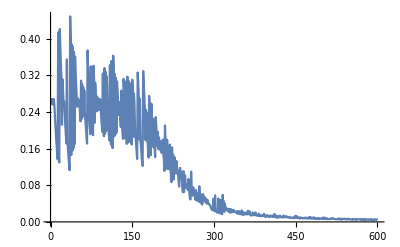

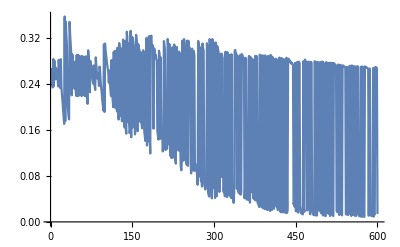

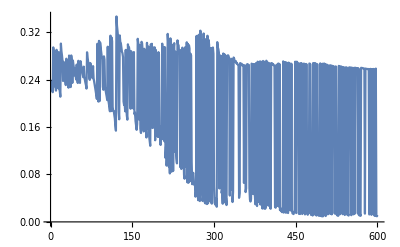

```mathematica
(* Fixed eta, experiment with different hidden layer sizes:*)
SeedRandom[42]; (* Make sure we have deterministic results *)
eta=1;
numIters=600;
testHiddenLayerSize[size_]:=ListPlot[backprop[9, size, 1,trainingData, eta, 600][[3]], Joined->True];

testHiddenLayerSize[10]
testHiddenLayerSize[8]
testHiddenLayerSize[6]
testHiddenLayerSize[4]
testHiddenLayerSize[3]
testHiddenLayerSize[2]
testHiddenLayerSize[1]
```

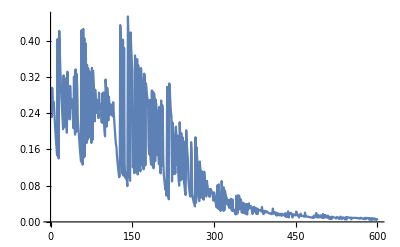

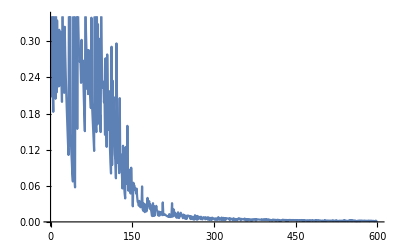

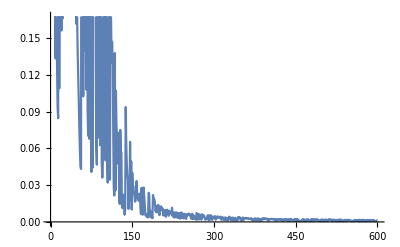

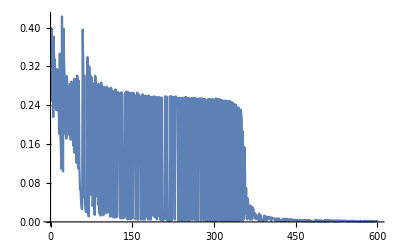

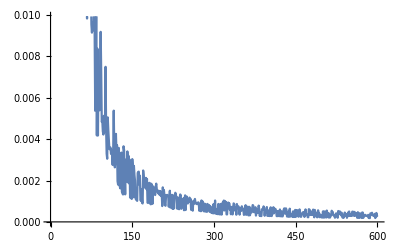

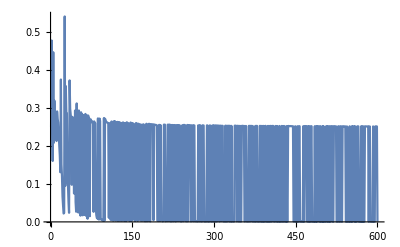

```mathematica
(*With eta = 1 and numIters = 600, the minimum hidden layer size that allowed convergence was 3*)
SeedRandom[42]; (* Make sure we have deterministic results *)
hiddenLayerSize = 3;
testEta[testEta_]:=ListPlot[backprop[9, hiddenLayerSize, 1,trainingData, testEta, 600][[3]], Joined->True];

testEta[1]
testEta[2]
testEta[3]
testEta[5]
testEta[7]
testEta[8]
```

```mathematica
(* With numIters=600,and hidden layer size=3, the max eta that allowed convergence was around 7 *)

(* Now we test on inputs *)
trainingData
outs = backprop[9, 3, 1,trainingData, 7, 600];
inputs=trainingData⟦;;,1⟧;
hidden=sigmoid[inputs.Transpose[outs⟦1⟧]];
outputs=sigmoid[hidden.Transpose[outs⟦2⟧]]
```

{{{0.9,0.9,0.9,0.1,0.9,0.1,0.1,0.9,0.1},0},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},0},{{0.1,0.9,0.1,0.1,0.9,0.1,0.9,0.9,0.9},0},{{0.9,0.1,0.1,0.9,0.9,0.9,0.9,0.1,0.1},0},{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},1},{{0.9,0.9,0.9,0.9,0.1,0.9,0.9,0.1,0.9},1},{{0.9,0.9,0.9,0.9,0.1,0.1,0.9,0.9,0.9},1},{{0.9,0.1,0.9,0.9,0.1,0.9,0.9,0.9,0.9},1}}

{{0.0207333},{0.018611},{0.0223927},{0.018611},{0.987548},{0.987078},{0.987548},{0.988296}}

With numIters = 600, and hidden layer size = 3, the max eta that allowed convergence was around 7

Supervised learning for classification using built-in functions

One of the challenges of testing neural network models is that the data often under-specifies the models--there are too many parameters to test, and there may be a large class of models that all give similar results. And without ways of testing or measuring these parameters, it makes sense to try simpler models first.  Two of the simpler and commonly used for supervised learning are the nearest neighbor classifier, and linear support vector machine classifiers. 

This exercise will provide experience with Mathematica’s built-in machine learning functions for doing classification. Most of the details of the algorithms are hidden, which helps to focus on concepts and develop high-level intuitions, but it can be frustrating if you want to better understand the details.  Use the Mathematica documentation for anything you don’t understand.

We revisit the T vs. C classification problem, but using Mathematica’s general purpose Classify[ ] function. Critically, we will test how well different classification methods, each trained on just a small number of rotations of two letters T and C, generalize to rotated, blurred versions.

The Classify methods are “discriminative”--they have no built-in knowledge of the specific underlying generative structure, i.e. in our case that training instances result from rotations in the plane.

Classify[] will accept image formatted data, which makes it easy to visualize the stimuli and results. The default measure of distance between images is EuclideanDistance[].

The exercise illustrates how different methods generalize differently as a consequence of the underlying data structure, and the range of training instances.

The first steps are already done. You will need to fill in  blanks beginning with “Set up and run a linear SVM classifier”. Later in the exercise you will need to change some parameters defining the training set.

#### Stimulus generation functions

```mathematica
Clear[Δangle,iTlist,iClist]
iTlist[Δangle_]:=Table[ImageRotate[Binarize[-Graphics-,.1],deg Degree, Full],{deg,0,360-Δangle,Δangle}];
iClist[Δangle_]:=Table[ImageRotate[Binarize[-Graphics-,.1],deg Degree, Full],{deg,0,360-Δangle,Δangle}];
```

#### First define the training set:

Note the syntax to set up a dictionary structure:
	Thread[{data1, data2, data3} -> {label1, label2, label3}]
	which outputs:
	{data1 -> label1, data2 -> label2, data3 -> label3}
	Use ConstantArray[] to fill the lists with the labels. And Join[] to concatenate both sets of training pairs.

```mathematica
SeedRandom[0];
```

```mathematica
Δangle0train =40; (*45 degree increments*)
{dim}=Dimensions[iTlist[Δangle0train]];
trainingset =Flatten[Join[{Thread[iTlist[Δangle0train]->ConstantArray["T",dim]],
Thread[iClist[Δangle0train]->ConstantArray["C",dim]]}]];
Dimensions@trainingset
trainingset[[2]]
```

{18}

-Graphics-→T

#### Second define a test set

To be used below to test for generalization beyond what the algorithm was trained on. The test set  includes novel rotations with slight blur.

```mathematica
Δangle0test =8;
{dim}=Dimensions[iTlist[Δangle0test ]];
testsetall=Flatten[Join[{Thread[iTlist[Δangle0test ]->ConstantArray["T",dim]],
Thread[iClist[Δangle0test ]->ConstantArray["C",dim]]}]];
(*Remove any elements that were part of the training set*)
testset0=Complement[testsetall,trainingset];
testset = Thread[Blur[#,8]&/@Keys@testset0->Values[testset0]];
testset [[1]]
```

-Graphics-→T

#### Set up and run a linear SVM classifier

A. Set up and run a linear support vector machine classifier

Fill in the missing function arguments.

```mathematica
csvm=Classify[trainingset,Method-> "SupportVectorMachine"];
```

B. Use the function, Information[csvm], to inspect the setup

```mathematica
Information[csvm]
```

Classifier information
Data type | Image
Classes | ,,CT
Accuracy | (50.7.) %
Method | SupportVectorMachine
Single evaluation time | 6.42 ms/example
Batch evaluation speed | 840. examples/s
Loss | 0.693 ± 0.028
Model memory | 1.1 MB
Training examples used | 18 examples
Training time | 8.03 s

C. Apply ClassifierMeasurements[] to testset to measure how well the model generalizes to rotations in the plane. Print out the accuracy and the confusion matrix.

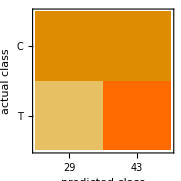
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 72
Accuracy | (60.6.) %
Accuracy baseline | (50.6.) %
Geometric mean of probabilities | 0.5 ± 8.3×10^-17
Mean cross entropy | 0.693 ± 1.1×10^-16
Single evaluation time | 6.51 ms/example
Batch evaluation speed | 512. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[csvm, testset]
```

#### Set up and run a nearest neighbors classifier with the same training set

D. Set up nearest neighbor classifier. As above, run, and output the accuracy and confusion matrix for the testset. Fill in the missing function arguments, then print out the accuracy and the confusion matrix.

```mathematica
cnn=Classify[trainingset,Method->"NearestNeighbors"];
```

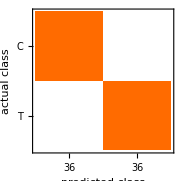
Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 72
Accuracy | (100.00000000000000022) %
Accuracy baseline | (50.6.) %
Geometric mean of probabilities | 0.833
Mean cross entropy | 0.182 ± 2.8×10^-17
Single evaluation time | 4.76 ms/example
Batch evaluation speed | 961. examples/s
-Graphics- |

```mathematica
cmnn=ClassifierMeasurements[cnn, testset];
cmnn
```

#### Plot accuracy as a function of number of exemplars stored for a fixed testset

Under some circumstances, we might expect that accuracy will increase if we have more exemplars stored in memory. In the exercise below, confirm that is true for the Nearest Neighbor classifier for our particular toy example and parameters. (In general,  we would want to vary the test set too.)

E. Make a plot of Nearest Neighbor accuracy vs. N, the number of exemplars in the trainingset.  
Leave Δangle0test = 8 fixed for the testset, and vary the number of exemplars in the trainingset by using these values of Δangle0train = {40,35,30,25, 20}.  It doesn’t matter exactly how you gather the numbers for the plot, e.g. writing a little routine, or interactively running the above cells, and noting the outputs.

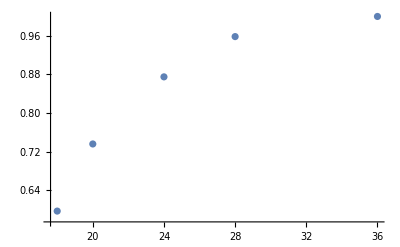

```mathematica
Δangle0trains = {40,35,30,25, 20};
plotInfo = {};
For[i=1, i<=5, i++,
Δangle0train =Δangle0trains[[i]];
{dim}=Dimensions[iTlist[Δangle0train]];
trainingset =Flatten[Join[{Thread[iTlist[Δangle0train]->ConstantArray["T",dim]],
Thread[iClist[Δangle0train]->ConstantArray["C",dim]]}]];
	cnn=Classify[trainingset,Method->"NearestNeighbors"];
	acc = ClassifierMeasurements[cnn, testset, "Accuracy"];
	accuracy = Append[accuracy, acc];
plotInfo = Append[plotInfo, {Length[trainingset], acc}]
];
ListPlot[plotInfo]
(* X axis is the number of examples in the training set. Y axis is the test set performance.*)
```